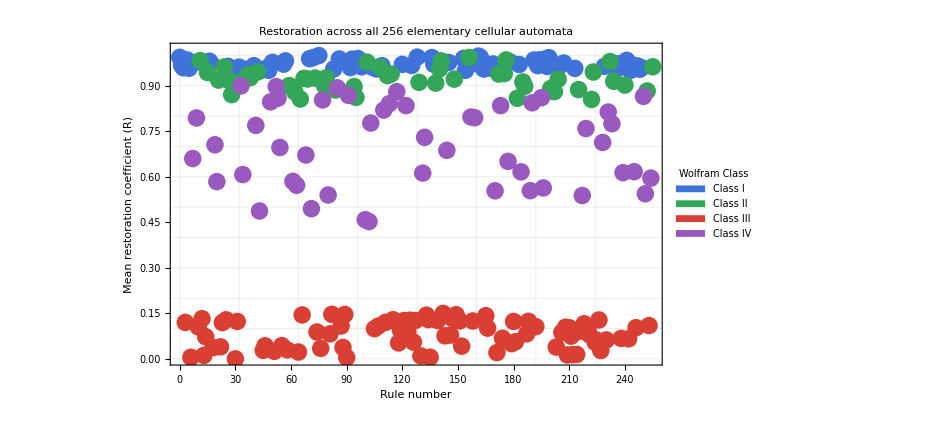

```mathematica
(* ::Section::*)(*Ruliological Resilience Plotting Utilities*)ClearAll["Global`*"];

(*-----------------------------------------*)
(*1. Example data structure*)
(*-----------------------------------------*)

(*Assumed format for all-rule summary data:allRuleResults={<|"Rule"->0,"Class"->1,"MeanR"->1.00,"StdR"->0.00|>,<|"Rule"->30,"Class"->3,"MeanR"->0.02,"StdR"->0.01|>,<|"Rule"->62,"Class"->2,"MeanR"->0.88,"StdR"->0.05|>,<|"Rule"->110,"Class"->4,"MeanR"->0.82,"StdR"->0.10|>,...};
If you already have CSV output,see the import section below.*)

(*Example placeholder data for testing*)
SeedRandom[1234];

exampleClass[rule_]:=Which[MemberQ[{0,4,8,32,40,128,136,160,168},rule],1,MemberQ[{62,73,108,232},rule],2,MemberQ[{18,22,30,45,90,105,126,150,225},rule],3,MemberQ[{54,110,184},rule],4,True,RandomChoice[{1,2,3,4}]];

exampleMeanR[class_]:=Which[class==1,RandomReal[{0.95,1.0}],class==2,RandomReal[{0.85,1.0}],class==3,RandomReal[{0.0,0.15}],class==4,RandomReal[{0.45,0.9}]];

exampleStdR[class_]:=Which[class==1,RandomReal[{0.0,0.02}],class==2,RandomReal[{0.01,0.06}],class==3,RandomReal[{0.0,0.03}],class==4,RandomReal[{0.05,0.12}]];

allRuleResults=Table[Module[{c=exampleClass[r]},<|"Rule"->r,"Class"->c,"MeanR"->exampleMeanR[c],"StdR"->exampleStdR[c]|>],{r,0,255}];

(*Force a few canonical values*)
allRuleResults=allRuleResults/. {a_Association/;a["Rule"]==30:><|"Rule"->30,"Class"->3,"MeanR"->0.00,"StdR"->0.01|>,a_Association/;a["Rule"]==62:><|"Rule"->62,"Class"->2,"MeanR"->0.88,"StdR"->0.05|>,a_Association/;a["Rule"]==110:><|"Rule"->110,"Class"->4,"MeanR"->0.82,"StdR"->0.10|>,a_Association/;a["Rule"]==232:><|"Rule"->232,"Class"->2,"MeanR"->0.98,"StdR"->0.02|>};

(*-----------------------------------------*)
(*2. Optional CSV import*)
(*-----------------------------------------*)

(*If you have a CSV like:Rule,Class,MeanR,StdR 0,1,1.0,0.0 30,3,0.0,0.01 62,2,0.88,0.05 110,4,0.82,0.10... use:allRuleResults=Import["/path/to/all_rule_results.csv","Dataset"]//Normal;*)

(*-----------------------------------------*)
(*3. Styling*)
(*-----------------------------------------*)

classColors=<|1->RGBColor[0.25,0.45,0.85],2->RGBColor[0.20,0.65,0.35],3->RGBColor[0.85,0.25,0.20],4->RGBColor[0.60,0.35,0.75]|>;

classLabels=<|1->"Class I",2->"Class II",3->"Class III",4->"Class IV"|>;

baseLabelStyle=Directive[Black,14];
titleStyle=Directive[Black,16,Bold];

legend=SwatchLegend[Values[classColors],Values[classLabels],LegendLabel->Style["Wolfram Class",13,Bold],LabelStyle->12];

(*-----------------------------------------*)
(*4. Helper functions*)
(*-----------------------------------------*)

getClassSubset[data_,class_]:=Select[data,#Class==class&];
getXY[data_]:=data[[All,{"Rule","MeanR"}]]/. a_Association:>{a["Rule"],a["MeanR"]};

(*-----------------------------------------*)
(*5. Figure 1:Scatter of Mean R by Rule*)
(*-----------------------------------------*)

scatterPlots=Table[With[{subset=getClassSubset[allRuleResults,c]},ListPlot[getXY[subset],PlotStyle->{classColors[c],PointSize[0.018]},PlotRange->{{0,255},{0,1.02}},Axes->False,Frame->True,FrameLabel->{Style["Rule number",baseLabelStyle],Style["Mean restoration coefficient (R)",baseLabelStyle]},LabelStyle->baseLabelStyle,ImageSize->700]],{c,1,4}];

fig1=Legended[Show[scatterPlots,PlotLabel->Style["Restoration across all 256 elementary cellular automata",titleStyle],GridLines->{Range[0,255,32],Range[0,1,0.1]},GridLinesStyle->Directive[GrayLevel[0.9],Thin]],Placed[legend,Right]];

Export["figure1_restoration_scatter.png",fig1,ImageResolution->300];
Export["figure1_restoration_scatter.pdf",fig1];

fig1
```

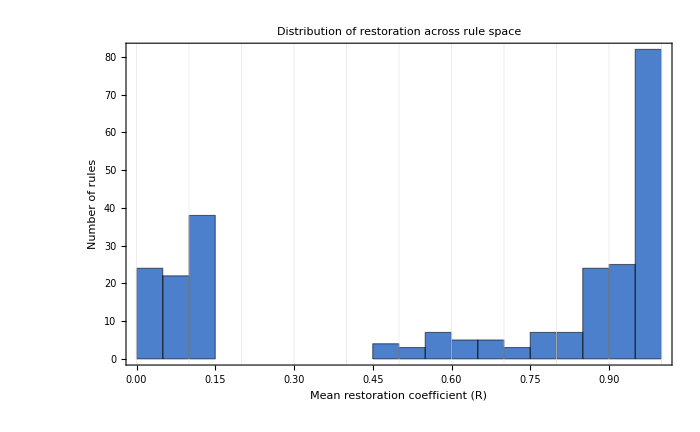

```mathematica
(*-----------------------------------------*)(*6. Figure 2:Histogram of Mean R*)(*-----------------------------------------*)meanRValues=allRuleResults[[All,"MeanR"]];

fig2=Histogram[meanRValues,{0,1,0.05},"Count",ChartStyle->RGBColor[0.3,0.5,0.8],Frame->True,Axes->False,FrameLabel->{Style["Mean restoration coefficient (R)",baseLabelStyle],Style["Number of rules",baseLabelStyle]},PlotLabel->Style["Distribution of restoration across rule space",titleStyle],LabelStyle->baseLabelStyle,GridLines->{Range[0,1,0.1],None},GridLinesStyle->Directive[GrayLevel[0.9],Thin],ImageSize->700];

Export["figure2_restoration_histogram.png",fig2,ImageResolution->300];
Export["figure2_restoration_histogram.pdf",fig2];

fig2
```

```mathematica
(*-----------------------------------------*)(*6. Figure 2:Histogram of Mean R*)(*-----------------------------------------*)meanRValues=allRuleResults[[All,"MeanR"]];

fig2=Histogram[meanRValues,{0,1,0.05},"Count",ChartStyle->RGBColor[0.3,0.5,0.8],Frame->True,Axes->False,FrameLabel->{Style["Mean restoration coefficient (R)",baseLabelStyle],Style["Number of rules",baseLabelStyle]},PlotLabel->Style["Distribution of restoration across rule space",titleStyle],LabelStyle->baseLabelStyle,GridLines->{Range[0,1,0.1],None},GridLinesStyle->Directive[GrayLevel[0.9],Thin],ImageSize->700];

Export["figure2_restoration_histogram.png",fig2,ImageResolution->300];
Export["figure2_restoration_histogram.pdf",fig2];

fig2
```

-Graphics-

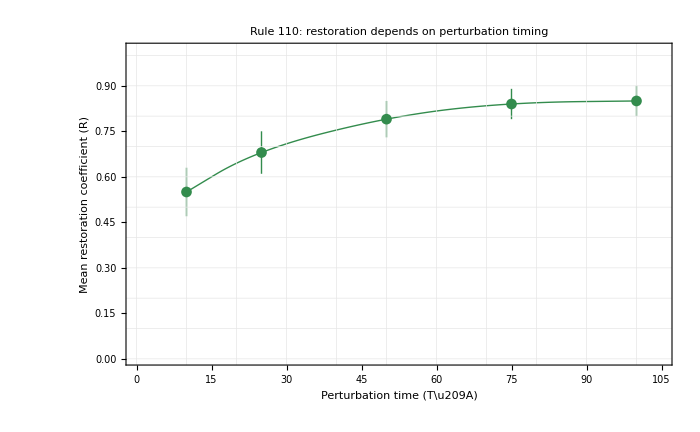

```mathematica
(*-----------------------------------------*)(*8. Example Rule 110 timing data*)(*-----------------------------------------*)rule110TimeData={<|"Time"->10,"MeanR"->0.55,"StdR"->0.08|>,<|"Time"->25,"MeanR"->0.68,"StdR"->0.07|>,<|"Time"->50,"MeanR"->0.79,"StdR"->0.06|>,<|"Time"->75,"MeanR"->0.84,"StdR"->0.05|>,<|"Time"->100,"MeanR"->0.85,"StdR"->0.05|>};

timeErrorBars=rule110TimeData/. a_Association:>{a["Time"],Around[a["MeanR"],a["StdR"]]};

fig4=ListLinePlot[timeErrorBars,Frame->True,Axes->False,FrameLabel->{Style["Perturbation time (T\u209A)",baseLabelStyle],Style["Mean restoration coefficient (R)",baseLabelStyle]},PlotLabel->Style["Rule 110: restoration depends on perturbation timing",titleStyle],PlotStyle->Directive[RGBColor[0.20,0.55,0.30],Thick],PlotMarkers->Automatic,InterpolationOrder->2,PlotRange->{{0,105},{0,1.02}},GridLines->{Range[0,100,10],Range[0,1,0.1]},GridLinesStyle->Directive[GrayLevel[0.9],Thin],LabelStyle->baseLabelStyle,ImageSize->700];

Export["figure4_rule110_timing.png",fig4,ImageResolution->300];
Export["figure4_rule110_timing.pdf",fig4];

fig4
```

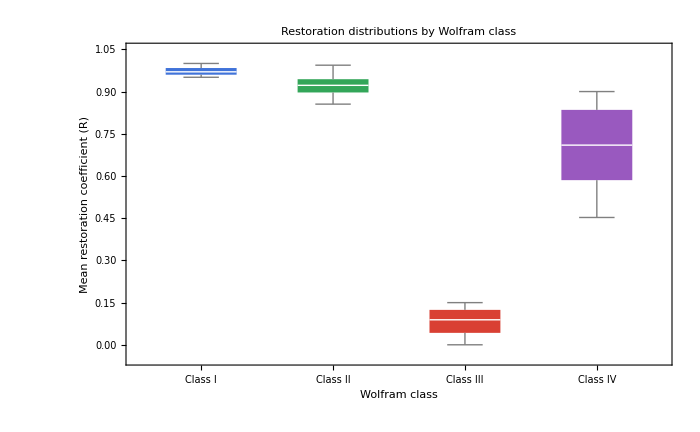

```mathematica
(*-----------------------------------------*)(*9. Figure 5:Box-whisker by class*)(*-----------------------------------------*)classGroupedR=Table[Select[allRuleResults,#Class==c&][[All,"MeanR"]],{c,1,4}];

fig5=BoxWhiskerChart[classGroupedR,ChartLabels->(Style[#,12]&/@Values[classLabels]),ChartStyle->Values[classColors],Frame->True,Axes->False,FrameLabel->{Style["Wolfram class",baseLabelStyle],Style["Mean restoration coefficient (R)",baseLabelStyle]},PlotLabel->Style["Restoration distributions by Wolfram class",titleStyle],LabelStyle->baseLabelStyle,ImageSize->700];

Export["figure5_class_boxplot.png",fig5,ImageResolution->300];
Export["figure5_class_boxplot.pdf",fig5];

fig5
```

```mathematica
trialData={<|"Rule"->110,"Class"->4,"Trial"->1,"R"->0.80|>,<|"Rule"->110,"Class"->4,"Trial"->2,"R"->0.84|>,<|"Rule"->30,"Class"->3,"Trial"->1,"R"->0.01|>
(*...*)};

ruleSummary=Values@KeySort@GroupBy[trialData,#Rule&,Function[group,<|"Rule"->group[[1,"Rule"]],"Class"->group[[1,"Class"]],"MeanR"->Mean[group[[All,"R"]]],"StdR"->StandardDeviation[group[[All,"R"]]]|>]];
```

StandardDeviation::shlen: The argument {0.01} should have at least two elements.

```mathematica
ClearAll["Global`*"];

(*---------------------------------------------------------Example data structure assumed:ruleSpaceData=list of associations with keys:"Rule","Entropy","MeanRfull","Class"---------------------------------------------------------*)

(*Top highlighted 1D rules*)
topRules={18,60,110,30};

(*Manual clam point*)
clamEntropy=0.75;
clamRfull=0.9829;

(*Colors*)
classColor[class_]:=Switch[class,"Simple periodic",RGBColor[0.4,0.55,0.9],"Chaotic fragile",RGBColor[0.85,0.45,0.45],"Structured robust",GrayLevel[0.55],"Fractal / nested",RGBColor[0.7,0.5,0.85],"Mixed / intermediate",GrayLevel[0.7],"Trivial sparse",GrayLevel[0.85],"Trivial full",GrayLevel[0.85],_,GrayLevel[0.7]];

(*Extract numeric coordinates*)
pts1D=ruleSpaceData/. a_Association:>{a["Entropy"],a["MeanRfull"]};

best1DR=Max[ruleSpaceData[[All,"MeanRfull"]]];

pts=Map[{#Entropy,#MeanRfull}&,ruleSpaceData]

upperBoundLine={Directive[Black,Dashed,Thick],Line[{{0.3,best1DR},{0.85,best1DR}}],Text[Style["1D restoration upper bound",12,Bold,Background->White],{0.6,best1DR+0.005}]};

(*Bounding rectangle for 1D cloud*)
xmin=Min[pts1D[[All,1]]]-0.01;
xmax=Max[pts1D[[All,1]]]+0.01;
ymin=Min[pts1D[[All,2]]]-0.01;
ymax=Max[pts1D[[All,2]]]+0.01;

(*Build graphics primitives*)
backgroundRegion={Directive[GrayLevel[0.92],Opacity[0.35]],Rectangle[{xmin,ymin},{xmax,ymax}]};

allPoints=ruleSpaceData/. a_Association:>{classColor[a["Class"]],PointSize[0.022],Point[{a["Entropy"],a["MeanRfull"]}]};

topPointLabels=ruleSpaceData/. a_Association:>If[MemberQ[topRules,a["Rule"]],{Red,PointSize[0.03],Point[{a["Entropy"],a["MeanRfull"]}],Text[Style[ToString[a["Rule"]],12,Bold,Background->White],{a["Entropy"],a["MeanRfull"]}+{0.006,0.003}]},Nothing];

best1DLine={Directive[Black,Dashed,Thickness[0.002]],Line[{{0.3,best1DR},{0.85,best1DR}}],Text[Style["best 1D restoration",11,Background->White],{0.62,best1DR+0.003}]};

oneDLabel={Text[Style["1D shell-like rule regime\n(complexity–repair tradeoff)",13,Bold,Background->White],{0.47,0.865}]};

dimensionalityArrow={Directive[Black,Thick],Arrow[{{0.6,0.84},{clamEntropy-0.01,clamRfull-0.01}}],Text[Style["Dimensionality unlocks higher restoration",12,Bold,Background->White],{0.62,0.92}]};

clamPoint={Red,PointSize[0.04],Point[{clamEntropy,clamRfull}],Text[Style["2D Rule 224\nBreaks 1D limit",14,Bold,Background->White],{clamEntropy+0.01,clamRfull+0.005}]};
finalPlot=Graphics[{backgroundRegion,allPoints,topPointLabels,best1DLine,oneDLabel,dimensionalityArrow,clamPoint},Frame->True,Axes->False,FrameLabel->{Style["Mean entropy (complexity)",16],Style["Mean post-injury restoration (Rfull)",16]},PlotRange->{{0.3,0.85},{0.72,1.0}},GridLines->Automatic,GridLinesStyle->Directive[GrayLevel[0.88]],ImageSize->950,PlotLabel->Style["Dimensionality separates complexity–repair regimes in rule space",18,Bold],BaseStyle->{FontFamily->"Helvetica"}];

finalPlot
```

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

ruleSpaceData

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

-Graphics-

```mathematica
(* ::Section::*)(*Ruliological Resilience:Full Computation Pipeline*)ClearAll["Global`*"];

(* =========================================*)
(*1. Core parameters*)
(* =========================================*)

defaultL=200;
defaultTotalSteps=300;
defaultRecoveryWindow=100;

(* =========================================*)
(*2. Utility:single-seed initial condition*)
(* =========================================*)

singleSeedInitialCondition[L_Integer?Positive]:=Module[{state=ConstantArray[0,L]},state[[Ceiling[L/2]]]=1;
state];

(* =========================================*)
(*3. Generate control trajectory*)
(* =========================================*)

controlEvolution[rule_Integer,L_Integer:defaultL,totalSteps_Integer:defaultTotalSteps,boundary_:"Periodic"]:=Module[{init,spec},init=singleSeedInitialCondition[L];
spec=If[boundary==="Periodic",{rule,2,1},{rule,1}];
CellularAutomaton[spec,init,totalSteps]];

(* =========================================*)
(*4. Injury operators*)
(* =========================================*)

randomMixInjury[state_List,center_Integer,width_Integer]:=Module[{injured=state,left,right,idx},left=Max[1,center-Floor[width/2]];
right=Min[Length[state],center+Ceiling[width/2]-1];
idx=Range[left,right];
injured[[idx]]=RandomInteger[{0,1},Length[idx]];
injured];

voidInjury[state_List,center_Integer,width_Integer]:=Module[{injured=state,left,right,idx},left=Max[1,center-Floor[width/2]];
right=Min[Length[state],center+Ceiling[width/2]-1];
idx=Range[left,right];
injured[[idx]]=0;
injured];

bitFlipInjury[state_List,center_Integer,width_Integer]:=Module[{injured=state,left,right,idx},left=Max[1,center-Floor[width/2]];
right=Min[Length[state],center+Ceiling[width/2]-1];
idx=Range[left,right];
injured[[idx]]=1-injured[[idx]];
injured];

applyInjury[state_List,injuryType_String,center_Integer,width_Integer]:=Switch[injuryType,"RandomMix",randomMixInjury[state,center,width],"Void",voidInjury[state,center,width],"BitFlip",bitFlipInjury[state,center,width],_,Message[applyInjury::badtype,injuryType];state];

applyInjury::badtype="Unknown injury type `1`. Valid types are RandomMix, Void, BitFlip.";

(* =========================================*)
(*5. Evolve one step manually*)
(* =========================================*)

nextState[state_List,rule_Integer,boundary_:"Periodic"]:=Module[{spec},spec=If[boundary==="Periodic",{rule,2,1},{rule,1}];
CellularAutomaton[spec,state,1][[-1]]];

(* =========================================*)
(*6. Paired control/injured trajectories*)
(* =========================================*)

pairedEvolution[rule_Integer,L_Integer:defaultL,totalSteps_Integer:defaultTotalSteps,perturbTime_Integer:50,width_Integer:20,injuryType_String:"RandomMix",boundary_:"Periodic"]:=Module[{control,injured,center,injuredStateAtTp,t},If[perturbTime<1||perturbTime>=totalSteps,Return[$Failed]];
control=controlEvolution[rule,L,totalSteps,boundary];
center=Ceiling[L/2];
injured=control[[1;;perturbTime]];
injuredStateAtTp=applyInjury[injured[[-1]],injuryType,center,width];
injured[[-1]]=injuredStateAtTp;
For[t=perturbTime+1,t<=totalSteps+1,t++,injured=Append[injured,nextState[injured[[-1]],rule,boundary]];];
<|"Rule"->rule,"L"->L,"TotalSteps"->totalSteps,"PerturbTime"->perturbTime,"Width"->width,"InjuryType"->injuryType,"Boundary"->boundary,"Control"->control,"Injured"->injured|>];

(* =========================================*)
(*7. Difference maps and divergence*)
(* =========================================*)

differenceMap[control_List,injured_List]:=MapThread[BitXor,{control,injured}];

normalizedDivergence[diffState_List]:=N[Total[diffState]/Length[diffState]];

divergenceSeries[control_List,injured_List]:=normalizedDivergence/@differenceMap[control,injured];

(* =========================================*)
(*8. Restoration coefficient definitions*)
(* =========================================*)

restorationCoefficient[control_List,injured_List,perturbTime_Integer,recoveryWindow_Integer:defaultRecoveryWindow]:=Module[{diffs,startIdx,endIdx,avgD},diffs=divergenceSeries[control,injured];
startIdx=perturbTime+2;
endIdx=Min[Length[diffs],perturbTime+1+recoveryWindow];
If[startIdx>endIdx,Return[Indeterminate]];
avgD=Mean[diffs[[startIdx;;endIdx]]];
1-avgD];

finalRestorationCoefficient[control_List,injured_List]:=Module[{diffs},diffs=divergenceSeries[control,injured];
1-Last[diffs]];

timeResolvedRestoration[control_List,injured_List]:=1-divergenceSeries[control,injured];

(* =========================================*)
(*9. Shift-tolerant restoration (optional)*)
(* =========================================*)

circularShift[list_List,k_Integer]:=RotateRight[list,k];

shiftTolerantDivergenceAtTime[controlState_List,injuredState_List,kmax_Integer:10]:=Module[{vals},vals=Table[normalizedDivergence[BitXor[controlState,circularShift[injuredState,k]]],{k,-kmax,kmax}];
Min[vals]];

shiftTolerantRestorationCoefficient[control_List,injured_List,perturbTime_Integer,recoveryWindow_Integer:defaultRecoveryWindow,kmax_Integer:10]:=Module[{startIdx,endIdx,avgD},startIdx=perturbTime+2;
endIdx=Min[Length[control],perturbTime+1+recoveryWindow];
If[startIdx>endIdx,Return[Indeterminate]];
avgD=Mean@Table[shiftTolerantDivergenceAtTime[control[[t]],injured[[t]],kmax],{t,startIdx,endIdx}];
1-avgD];

(* =========================================*)
(*10. Restoration time*)
(* =========================================*)

restorationTime[control_List,injured_List,perturbTime_Integer,epsilon_:0.01,sustain_:5]:=Module[{diffs,idx,window},diffs=divergenceSeries[control,injured];
For[idx=perturbTime+2,idx<=Length[diffs]-sustain+1,idx++,window=diffs[[idx;;idx+sustain-1]];
If[Max[window]<=epsilon,Return[idx-(perturbTime+1)]];];
Infinity];

(* =========================================*)
(*11. Single-run wrapper*)
(* =========================================*)

singleRunMetrics[rule_Integer,L_Integer:defaultL,totalSteps_Integer:defaultTotalSteps,perturbTime_Integer:50,width_Integer:20,injuryType_String:"RandomMix",boundary_:"Periodic",recoveryWindow_Integer:defaultRecoveryWindow]:=Module[{sim,control,injured,R,Rfinal,Rshift,tau},sim=pairedEvolution[rule,L,totalSteps,perturbTime,width,injuryType,boundary];
If[sim===$Failed,Return[$Failed]];
control=sim["Control"];
injured=sim["Injured"];
R=restorationCoefficient[control,injured,perturbTime,recoveryWindow];
Rfinal=finalRestorationCoefficient[control,injured];
Rshift=shiftTolerantRestorationCoefficient[control,injured,perturbTime,recoveryWindow,10];
tau=restorationTime[control,injured,perturbTime,0.01,5];
Join[KeyDrop[sim,{"Control","Injured"}],<|"R"->R,"RFinal"->Rfinal,"RShift"->Rshift,"RestorationTime"->tau|>]];

(* =========================================*)
(*12. Multi-trial execution*)
(* =========================================*)

multiTrialMetrics[rule_Integer,nTrials_Integer:50,L_Integer:defaultL,totalSteps_Integer:defaultTotalSteps,perturbTime_Integer:50,width_Integer:20,injuryType_String:"RandomMix",boundary_:"Periodic",recoveryWindow_Integer:defaultRecoveryWindow]:=Table[Join[<|"Trial"->trial|>,singleRunMetrics[rule,L,totalSteps,perturbTime,width,injuryType,boundary,recoveryWindow]],{trial,1,nTrials}];

(* =========================================*)
(*13. Summarize one rule*)
(* =========================================*)

summarizeRuleTrials[trialResults_List,class_:Missing["NotAvailable"]]:=Module[{rule,Rs,Rfs,Rstars,tausFinite},rule=trialResults[[1,"Rule"]];
Rs=trialResults[[All,"R"]];
Rfs=trialResults[[All,"RFinal"]];
Rstars=trialResults[[All,"RShift"]];
tausFinite=Select[trialResults[[All,"RestorationTime"]],NumericQ[#]&&#=!=Infinity&];
<|"Rule"->rule,"Class"->class,"NTrials"->Length[trialResults],"MeanR"->Mean[Rs],"StdR"->StandardDeviation[Rs],"MeanRFinal"->Mean[Rfs],"StdRFinal"->StandardDeviation[Rfs],"MeanRShift"->Mean[Rstars],"StdRShift"->StandardDeviation[Rstars],"MeanRestorationTime"->If[Length[tausFinite]>0,Mean[tausFinite],Infinity],"MedianRestorationTime"->If[Length[tausFinite]>0,Median[tausFinite],Infinity]|>];

(* =========================================*)
(*14. Wolfram class lookup*)
(* =========================================*)

(*Replace this with your preferred class mapping.For now,this is a placeholder association for key canonical rules.*)

wolframClassAssociation=<|30->3,54->4,62->2,90->3,110->4,150->3,184->4,232->2|>;

getWolframClass[rule_Integer]:=Lookup[wolframClassAssociation,rule,Missing["Unknown"]];

(* =========================================*)
(*15. Run a batch of rules*)
(* =========================================*)

runRuleBatch[rules_List,nTrials_Integer:50,L_Integer:defaultL,totalSteps_Integer:defaultTotalSteps,perturbTime_Integer:50,width_Integer:20,injuryType_String:"RandomMix",boundary_:"Periodic",recoveryWindow_Integer:defaultRecoveryWindow]:=Module[{trialData,summaries},Print["Running ",Length[rules]," rules x ",nTrials," trials..."];
trialData=Flatten[Table[multiTrialMetrics[rule,nTrials,L,totalSteps,perturbTime,width,injuryType,boundary,recoveryWindow],{rule,rules}],1];
summaries=Table[With[{subset=Select[trialData,#Rule==rule&]},summarizeRuleTrials[subset,getWolframClass[rule]]],{rule,rules}];
<|"TrialData"->trialData,"RuleSummary"->summaries|>];

(* =========================================*)
(*16. Example run:canonical rules*)
(* =========================================*)

canonicalRules={30,62,110,232};

exampleBatch=runRuleBatch[canonicalRules,20,(*fewer trials for quick testing*)200,(*L*)250,(*totalSteps*)50,(*perturbTime*)20,(*width*)"RandomMix",(*injuryType*)"Periodic",(*boundary*)100              (*recovery window*)];

trialData=exampleBatch["TrialData"];
ruleSummary=exampleBatch["RuleSummary"];

Dataset[ruleSummary]
```

Running 4 rules x 20 trials...

```mathematica
Export["trial_data.csv",trialData];
Export["rule_summary.csv",ruleSummary];
```

```mathematica
sim110=pairedEvolution[110,200,250,50,20,"RandomMix","Periodic"];

control110=sim110["Control"];
injured110=sim110["Injured"];
diff110=differenceMap[control110,injured110];

controlPlot=ArrayPlot[control110,PixelConstrained->4,Frame->True,ImageSize->350,PlotLabel->Style["Rule 110 Control",14,Bold]];

injuredPlot=ArrayPlot[injured110,PixelConstrained->4,Frame->True,ImageSize->350,PlotLabel->Style["Rule 110 Injured",14,Bold]];

diffPlot=ArrayPlot[diff110,PixelConstrained->4,Frame->True,ImageSize->350,PlotLabel->Style["Rule 110 Difference Map",14,Bold]];

GraphicsRow[{controlPlot,injuredPlot,diffPlot},Spacings->15]
```

-Graphics-

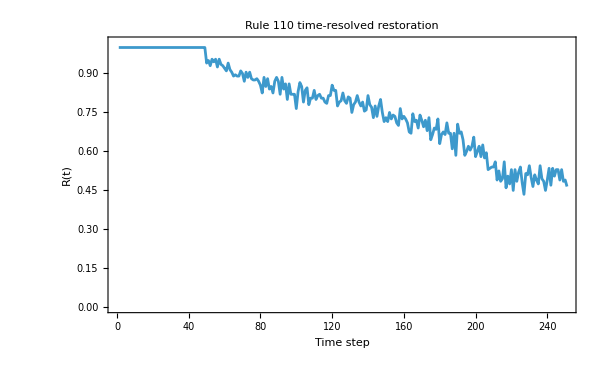

```mathematica
rSeries110=timeResolvedRestoration[control110,injured110];

ListLinePlot[rSeries110,Frame->True,Axes->False,PlotRange->{0,1.02},FrameLabel->{"Time step","R(t)"},PlotLabel->Style["Rule 110 time-resolved restoration",14,Bold],ImageSize->600]
```

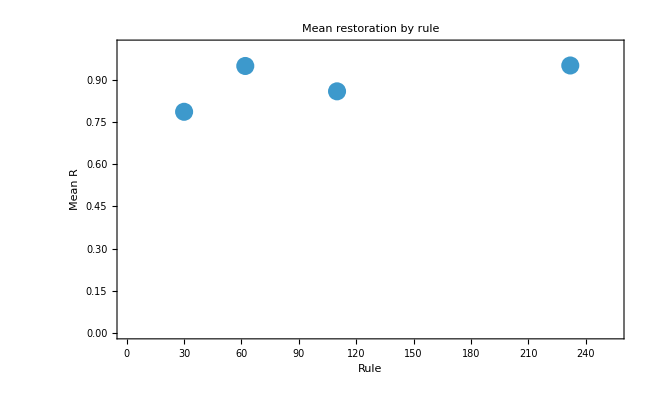

```mathematica
ListPlot[ruleSummary[[All,{"Rule","MeanR"}]]/. a_Association:>{a["Rule"],a["MeanR"]},Frame->True,Axes->False,PlotRange->{{0,255},{0,1.02}},FrameLabel->{"Rule","Mean R"},PlotLabel->Style["Mean restoration by rule",14,Bold],PlotStyle->Directive[PointSize[0.02]],ImageSize->650]
```

```mathematica
fullBatch=runRuleBatch[Range[0,255],50,200,300,50,20,"RandomMix","Periodic",100];

Export["full_trial_data.csv",fullBatch["TrialData"]];
Export["full_rule_summary.csv",fullBatch["RuleSummary"]];
```

Running 256 rules x 50 trials...

```mathematica
rule110WidthData={{"Width"->10,"MeanR"->0.85},{"Width"->20,"MeanR"->0.70},{"Width"->40,"MeanR"->0.25}};

widthPlot=ListLinePlot[rule110WidthData/. a_Association:>{a["Width"],a["MeanR"]},Frame->True,Axes->False,FrameLabel->{"Perturbation width (W)","Mean restoration (R)"},PlotLabel->Style["Rule 110: critical injury threshold",14,Bold],PlotMarkers->Automatic,PlotRange->{0,1.02},ImageSize->600];
```

ListLinePlot::optx: Unknown option Width→10 in ListLinePlot[{{Width→10,MeanR→0.85},{Width→20,MeanR→0.7},{Width→40,MeanR→0.25}},Frame→True,Axes→False,FrameLabel→{Perturbation width (W),Mean restoration (R)},PlotLabel→Rule 110: critical injury threshold,PlotMarkers→Automatic,PlotRange→{0,1.02},ImageSize→600].

Select::normal: Nonatomic expression expected at position 1 in Select[allRuleResults,#Class==c&].

Part::pspec1: Part specification MeanR is not applicable.

Histogram::ldata: Select[allRuleResults,#Class==c&]⟦All,MeanR⟧ is not a valid dataset or list of datasets.

Select::normal: Nonatomic expression expected at position 1 in Select[allRuleResults,#Class==c&].

Part::pspec1: Part specification MeanR is not applicable.

Histogram::ldata: Select[allRuleResults,#Class==c&]⟦All,MeanR⟧ is not a valid dataset or list of datasets.

Select::normal: Nonatomic expression expected at position 1 in Select[allRuleResults,#Class==c&].

General::stop: Further output of Select::normal will be suppressed during this calculation.

Part::pspec1: Part specification MeanR is not applicable.

General::stop: Further output of Part::pspec1 will be suppressed during this calculation.

Histogram::ldata: Select[allRuleResults,#Class==c&]⟦All,MeanR⟧ is not a valid dataset or list of datasets.

General::stop: Further output of Histogram::ldata will be suppressed during this calculation.

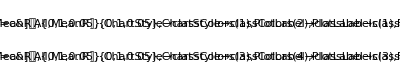

```mathematica
histByClass=Table[Histogram[Select[allRuleResults,#Class==c&][[All,"MeanR"]],{0,1,0.05},ChartStyle->classColors[c],PlotLabel->classLabels[c],Frame->True,Axes->False,ImageSize->400],{c,1,4}];

GraphicsGrid[Partition[histByClass,2]]
```

```mathematica
ListPlot[ruleSpaceData/. a_Association:>{a["Entropy"],a["MeanRfull"]},Frame->True,Axes->False,FrameLabel->{"Entropy (complexity)","Restoration (R)"},PlotStyle->PointSize[0.02],PlotLabel->Style["Complexity–Repair Phase Diagram",16,Bold],ImageSize->700]
```

ListPlot::lpn: ruleSpaceData is not a list of numbers or pairs of numbers.

ListPlot[ruleSpaceData,Frame→True,Axes→False,FrameLabel→{Entropy (complexity),Restoration (R)},PlotStyle→PointSize[0.02],PlotLabel→Complexity–Repair Phase Diagram,ImageSize→700]

```mathematica
pts=Map[{#Entropy,#MeanRfull}&,ruleSpaceData];

best1DR=Max[pts[[All,2]]];

Show[ListPlot[pts,PlotStyle->Directive[Black,PointSize[0.02]],Frame->True,Axes->False,FrameLabel->{"Mean entropy (complexity)","Mean restoration (Rfull)"},PlotRange->{{0.3,0.85},{0.72,1.0}},ImageSize->800],Graphics[{(*Upper bound*){Black,Dashed,Thick,Line[{{0.3,best1DR},{0.85,best1DR}}]},(*2D point*){Red,PointSize[0.04],Point[{clamEntropy,clamRfull}]},(*Annotation*)Text[Style["2D Rule 224 breaks 1D limit",14,Bold],{clamEntropy+0.02,clamRfull}],(*Arrow*)Arrow[{{0.6,0.84},{clamEntropy,clamRfull}}]}],PlotLabel->Style["Dimensionality separates complexity–repair regimes",16,Bold]]
```

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

ListPlot::lpn: ruleSpaceData is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListPlot[ruleSpaceData,PlotStyle→Directive[color,PointSize[0.02]],Frame→True,Axes→False,FrameLabel→{Mean entropy (complexity),Mean restoration (Rfull)},PlotRange→{{0.3,0.85},{0.72,1.}},ImageSize→800],,PlotLabel→Dimensionality separates complexity–repair regimes].

Show[ListPlot[ruleSpaceData,PlotStyle→Directive[GrayLevel[0],PointSize[0.02]],Frame→True,Axes→False,FrameLabel→{Mean entropy (complexity),Mean restoration (Rfull)},PlotRange→{{0.3,0.85},{0.72,1.}},ImageSize→800],-Graphics-,PlotLabel→Dimensionality separates complexity–repair regimes]

```mathematica
(*Example structure for one row*)<|"Rule"->110,"Class"->"IV","MeanR"->0.82,"StdR"->0.09,"MeanRFinal"->0.76,"MeanRShift"->0.93,"MeanTRest"->58.4|>
```

<|Rule→110,Class→IV,MeanR→0.82,StdR→0.09,MeanRFinal→0.76,MeanRShift→0.93,MeanTRest→58.4|>

```mathematica
(*---Group by class---*)classGroups=GroupBy[ruleSummaries,#Class&];

(*---Compute class-level summary stats---*)
classStats=AssociationMap[Function[group,Module[{vals=group[[All,"MeanR"]]},<|"NRules"->Length[vals],"MeanOfMeanR"->Mean[vals],"StdOfMeanR"->StandardDeviation[vals],"MedianOfMeanR"->Median[vals],"MinOfMeanR"->Min[vals],"MaxOfMeanR"->Max[vals]|>]],classGroups];

classStatsDataset=Dataset[KeyValueMap[Join[<|"Class"->#1|>,#2]&,classStats]];

classStatsDataset
```

GroupBy::list1: The argument ruleSummaries is not a valid list of Associations or rules or lists of rules.

AssociationMap::invrp: The argument GroupBy[ruleSummaries,#Class&] is not a valid Association or a list.

KeyValueMap::invak: The argument AssociationMap[Function[group,Module[{vals=group⟦All,MeanR⟧},Association[NRules→Length[vals],MeanOfMeanR→Mean[vals],StdOfMeanR→StandardDeviation[vals],MedianOfMeanR→Median[vals],MinOfMeanR→Min[vals],MaxOfMeanR→Max[vals]]]],GroupBy[ruleSummaries,#Class&]] is not a valid Association.

```mathematica
anovaData=Flatten[KeyValueMap[Function[{cls,rows},({cls,#["MeanR"]}&)/@rows],classGroups],1];

(*Preview*)
Take[anovaData,10]
```

KeyValueMap::invak: The argument GroupBy[ruleSummaries,#Class&] is not a valid Association.

Take::take: Cannot take positions 1 through 10 in KeyValueMap[Function[{cls,rows},({cls,#1[MeanR]}&)/@rows],GroupBy[ruleSummaries,#Class&]].

Take[KeyValueMap[Function[{cls,rows},({cls,#1[MeanR]}&)/@rows],GroupBy[ruleSummaries,#Class&]],10]

```mathematica
Needs["HypothesisTesting`"]

anovaResult=ANOVA[anovaData]
```

ANOVA[KeyValueMap[Function[{cls,rows},({cls,#1[MeanR]}&)/@rows],GroupBy[ruleSummaries,#Class&]]]

```mathematica
pairs=Subsets[classOrder,{2}];

pairwiseTests=Table[Module[{c1=pair[[1]],c2=pair[[2]],g1,g2,p},g1=classGroups[c1][[All,"MeanR"]];
g2=classGroups[c2][[All,"MeanR"]];
p=TTest[{g1,g2},"PValue"];
<|"Class1"->c1,"Class2"->c2,"PValue"->p|>],{pair,pairs}];

pairwiseDataset=Dataset[pairwiseTests];
pairwiseDataset
```

Subsets::normal: Nonatomic expression expected at position 1 in Subsets[classOrder,{2}].

Table::iterb: Iterator {pair,Subsets[classOrder,{2}]} does not have appropriate bounds.

```mathematica
classStats
```

AssociationMap[Function[group,Module[{vals=group⟦All,MeanR⟧},Association[NRules→Length[vals],MeanOfMeanR→Mean[vals],StdOfMeanR→StandardDeviation[vals],MedianOfMeanR→Median[vals],MinOfMeanR→Min[vals],MaxOfMeanR→Max[vals]]]],GroupBy[ruleSummaries,#Class&]]

```mathematica
ruleSummaries=fullBatch["RuleSummary"];
```

```mathematica
Head[ruleSummaries]
Length[ruleSummaries]
First[ruleSummaries]
Keys[GroupBy[ruleSummaries,#Class&]]
```

List

256

<|Rule→0,Class→Missing[Unknown],NTrials→50,MeanR→1.,StdR→0.,MeanRFinal→1.,StdRFinal→0.,MeanRShift→1.,StdRShift→0.,MeanRestorationTime→1,MedianRestorationTime→1|>

{Missing[Unknown],3,4,2}

```mathematica
knownRuleSummaries=Select[ruleSummaries,IntegerQ[#Class]&];
```

```mathematica
classGroups=GroupBy[knownRuleSummaries,#Class&];
classOrder=Sort[Keys[classGroups]];

classStats=AssociationMap[Function[group,Module[{vals=group[[All,"MeanR"]]},<|"NRules"->Length[vals],"MeanOfMeanR"->Mean[vals],"StdOfMeanR"->StandardDeviation[vals],"MedianOfMeanR"->Median[vals],"MinOfMeanR"->Min[vals],"MaxOfMeanR"->Max[vals]|>]],classGroups];

classStats//Dataset
```

Part::pspec1: Part specification MeanR is not applicable.

General::stop: Further output of Part::pspec1 will be suppressed during this calculation.

```mathematica
Needs["HypothesisTesting`"]

anovaGroups=(classGroups[#][[All,"MeanR"]]&)/@classOrder;

VectorQ[Flatten[anovaGroups],NumericQ]

anovaResult=ANOVA[anovaGroups]
```

True

ANOVA[{{0.952711,0.952699},{0.782112,0.793322,0.737882},{0.81636,0.852499,0.9498}}]

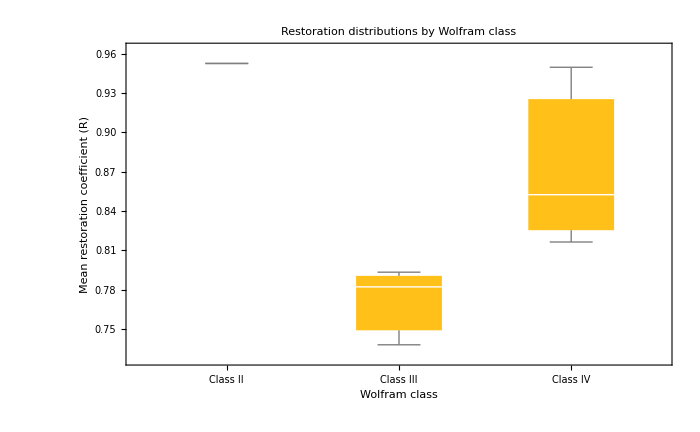

```mathematica
classLabels=<|2->"Class II",3->"Class III",4->"Class IV"|>;

figBox=BoxWhiskerChart[(classGroups[#][[All,"MeanR"]]&)/@classOrder,ChartLabels->(classLabels/@classOrder),Frame->True,Axes->False,FrameLabel->{"Wolfram class","Mean restoration coefficient (R)"},PlotLabel->Style["Restoration distributions by Wolfram class",14,Bold],ImageSize->700];

figBox
Export["restoration_boxplot_known_classes.png",figBox,ImageResolution->300];
```

```mathematica
StandardDeviation[classGroups[2][[All,"MeanR"]]]
Mean[classGroups[2][[All,"MeanR"]]]
```

8.48528×10^-6

0.952705

BoxWhiskerChart::chelfn: The value of the option ChartElementFunction -> BoxWhiskerChart is not a valid chart element function or an appropriate ChartElementData entity.

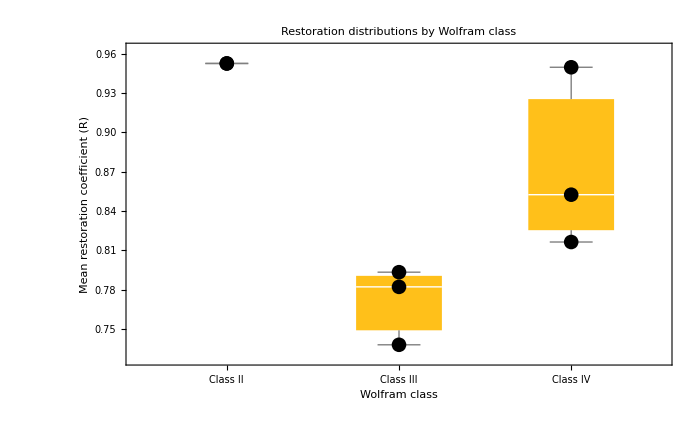

```mathematica
figBox=BoxWhiskerChart[(classGroups[#][[All,"MeanR"]]&)/@classOrder,ChartLabels->(classLabels/@classOrder),Frame->True,Axes->False,FrameLabel->{"Wolfram class","Mean restoration coefficient (R)"},PlotLabel->Style["Restoration distributions by Wolfram class",14,Bold],ImageSize->700,ChartElementFunction->"BoxWhiskerChart",Method->{"ShowOutliers"->True}];

(*overlay points*)
points=Table[With[{vals=classGroups[classOrder[[i]]][[All,"MeanR"]]},{Black,PointSize[0.015],Point[Transpose[{ConstantArray[i,Length[vals]],vals}]]}],{i,Length[classOrder]}];

Show[figBox,Graphics[points]]
```

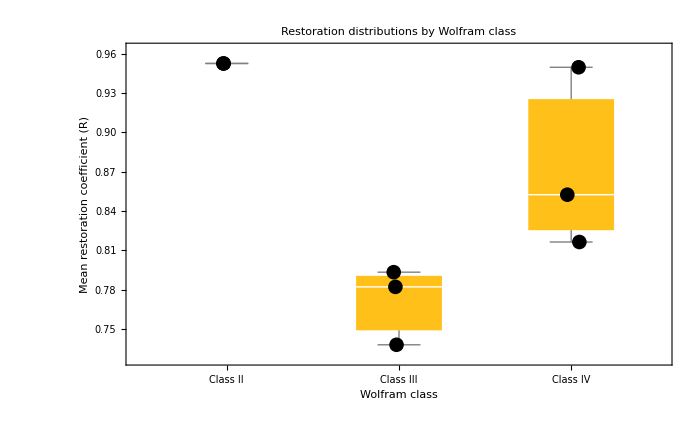

```mathematica
points=Table[With[{vals=classGroups[classOrder[[i]]][[All,"MeanR"]]},{Black,PointSize[0.015],Point[Transpose[{i+RandomReal[{-0.05,0.05},Length[vals]],vals}]]}],{i,Length[classOrder]}];

Show[figBox,Graphics[points]]
```